## The Laplace Transform and Applications Section 7.1 Exercises 1. (i)

```mathematica
f[t_]:=ToExpression["4+t^5+\\sin(5t) - 7\\cos(3t)", TeXForm]
```

```mathematica
f[t]
```

4+t^5-7 Cos[3 t]+Sin[5 t]

```mathematica
LaplaceTransform[f[t], t,s]
```

120/s^6+4/s-(7 s)/(9+s^2)+5/(25+s^2)

```mathematica
TeXForm[%]
```

\frac{120}{s^6}-\frac{7 s}{s^2+9}+\frac{5}{s^2+25}+\frac{4}{s}

## (ii)

```mathematica
f[t_]:=Exp[-11t]+Exp[t]*Sin[3t]+Exp[t-3]*HeavisideTheta[t-3]
```

```mathematica
f[t]
```

ⅇ^(-11 t)+ⅇ^(-3+t) HeavisideTheta[-3+t]+ⅇ^t Sin[3 t]

```mathematica
LaplaceTransform[f[t],t,s]
```

3/(9+(-1+s)^2)+ⅇ^(-3 s)/(-1+s)+1/(11+s)

```mathematica
TeXForm[%]
```

\frac{e^{-3 s}}{s-1}+\frac{1}{s+11}+\frac{3}{(s-1)^2+9}

## (iii)

```mathematica
f[t_]:=Exp[α*t](A*Cos[β*t]+ B* Sin[β*t])
```

```mathematica
f[t]
```

ⅇ^(t α) (A Cos[t β]+B Sin[t β])

```mathematica
LaplaceTransform[f[t], t,s]
```

(A (s-α))/((s-α)^2+β^2)+(B β)/((s-α)^2+β^2)

```mathematica
TextForm[%]
```

A (s - α)          B β
------------- + -------------
       2    2          2    2
(s - α)  + β    (s - α)  + β

## (iv)

```mathematica
f[t_]:= Exp[7t]*DiracDelta[t-3]
```

```mathematica
f[t]
```

ⅇ^(7 t) DiracDelta[-3+t]

```mathematica
LaplaceTransform[f[t], t,s]
```

ⅇ^(21-3 s)

## (v)

```mathematica
f[t_]:= Sum[DiracDelta[t-7k],{k, 0, Infinity}]
```

```mathematica
f[t]
```

∑_(k=0)^∞ DiracDelta[-7 k+t]

```mathematica
LaplaceTransform[f[t], t,s]
```

ⅇ^(7 s)/(-1+ⅇ^(7 s))

## 2. (i)

```mathematica
f[t_]:=Piecewise[{{3,t<=2},{0,t>2}}]
```

```mathematica
f[t]
```

Piecewise[{{3, t≤2}, {0, True}}]

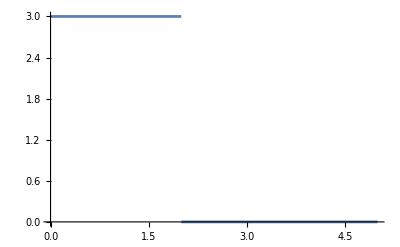

```mathematica
Plot[f[t], {t, 0, 5}]
```

```mathematica
LaplaceTransform[f[t], t,s]
```

(3 ⅇ^(-2 s) (-1+ⅇ^(2 s)))/s

```mathematica
Simplify[%]
```

(3-3 ⅇ^(-2 s))/s

```mathematica
TeXForm[%]
```

\frac{3-3 e^{-2 s}}{s}

## (ii)

```mathematica
f[t_]:=Piecewise[{{0,t<=2},{3,t>2}}]
```

```mathematica
f[t]
```

Piecewise[{{0, t≤2}, {3, t>2}, {0, True}}]

```mathematica
LaplaceTransform[f[t], t,s]
```

(3 ⅇ^(-2 s))/s

```mathematica
TeXForm[%]
```

\frac{3 e^{-2 s}}{s}

## (iii)

```mathematica
f[t_]:=Piecewise[{{Exp[2t],t<=2},{0,t>2}}]
```

```mathematica
f[t]
```

Piecewise[{{ⅇ^(2 t), t≤2}, {0, True}}]

```mathematica
LaplaceTransform[f[t], t,s]
```

(ⅇ^(-2 s) (-ⅇ^4+ⅇ^(2 s)))/(-2+s)

```mathematica
TeXForm[%]
```

\frac{e^{-2 s} \left(e^{2 s}-e^4\right)}{s-2}

## (iv)

```mathematica
f[t_]:=Piecewise[{{Exp[2t]*Sin[t],t<=Pi},{0,t>Pi}}]
```

```mathematica
f[t]
```

Piecewise[{{ⅇ^(2 t) Sin[t], t≤π}, {0, True}}]

```mathematica
LaplaceTransform[f[t],t,s]
```

(ⅇ^(-π (-2+s)) (1+ⅇ^(π (-2+s))))/(5-4 s+s^2)

```mathematica
TeXForm[%]
```

\frac{e^{-\pi  (s-2)} \left(e^{\pi  (s-2)}+1\right)}{s^2-4 s+5}

## (v)

```mathematica
f[t_]:=Piecewise[{{Exp[2t],1<=t<=4},{0, t<1 Or t>4}}]
```

```mathematica
f[t]
```

Piecewise[{{ⅇ^(2 t), 1≤t≤4}, {0, True}}]

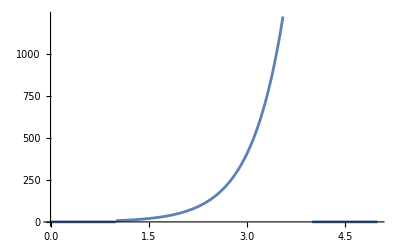

```mathematica
Plot[f[t], {t,0, 5}]
```

```mathematica
LaplaceTransform[f[t], t,s]
```

(ⅇ^(2-4 s) (-ⅇ^6+ⅇ^(3 s)))/(-2+s)

```mathematica
(ⅇ^(2-4 s) (-ⅇ^6+ⅇ^(3 s)))/(-2+s)
Simplify[%]
```

(ⅇ^(2-4 s) (-ⅇ^6+ⅇ^(3 s)))/(-2+s)

(ⅇ^(2-4 s) (-ⅇ^6+ⅇ^(3 s)))/(-2+s)

```mathematica
Distribute[%]
```

-ⅇ^(8-4 s)/(-2+s)+ⅇ^(2-s)/(-2+s)

```mathematica
TeXForm[%]
```

\frac{e^{2-s}}{s-2}-\frac{e^{8-4 s}}{s-2}

## (vi)

```mathematica
f[t_]:=Piecewise[{{0,1<=t<2 },{2, 2<=t<4},{0, 4<=t<6},{4, 6<=t}}]
```

```mathematica
f[t]
```

Piecewise[{{0, 1≤t<2}, {2, 2≤t<4}, {0, 4≤t<6}, {4, 6≤t}, {0, True}}]

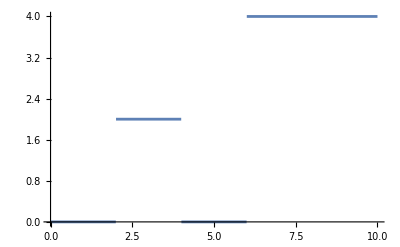

```mathematica
Plot[f[t], {t, 0, 10}]
```

```mathematica
LaplaceTransform[f[t], t,s]
```

(4 ⅇ^(-6 s) (1+ⅇ^(3 s) Sinh[s]))/s

```mathematica
Expand[%]
```

(4 ⅇ^(-6 s))/s+(4 ⅇ^(-3 s) Sinh[s])/s

```mathematica
TeXForm[%]
```

\frac{4 e^{-6 s}}{s}+\frac{4 e^{-3 s} \sinh (s)}{s}

## (vii)

```mathematica
f[t_]:=Piecewise[{{Exp[t],0<=t<=Pi},{Sin[t], t>=Pi}}]
```

```mathematica
f[t]
```

Piecewise[{{ⅇ^t, 0≤t≤π}, {Sin[t], t≥π}, {0, True}}]

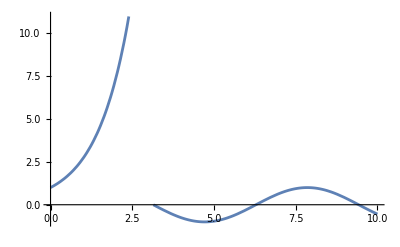

```mathematica
Plot[f[t], {t, 0, 10}]
```

```mathematica
LaplaceTransform[f[t], t,s]
```

(ⅇ^(-π s) (1-ⅇ^π+ⅇ^(π s)-s-ⅇ^π s^2+ⅇ^(π s) s^2))/((-1+s) (1+s^2))

```mathematica
Simplify[%]
```

(ⅇ^(-π s) (1-s-ⅇ^π (1+s^2)+ⅇ^(π s) (1+s^2)))/((-1+s) (1+s^2))

```mathematica
TeXForm[%]
```

\frac{e^{-\pi  s} \left(e^{\pi  s} \left(s^2+1\right)-e^{\pi } \left(s^2+1\right)-s+1\right)}{(s-1) \left(s^2+1\right)}

```mathematica
LaplaceTransform[Sin[t]/t, t,s]
```

ArcTan[1/s]

## 3. (i)

```mathematica
F[s_]:=1/(s(s+1))
```

```mathematica
F[s]
```

1/(s (1+s))

```mathematica
InverseLaplaceTransform[F[s],s,t]
```

1-ⅇ^-t

## (ii)

```mathematica
F[s_]:=s/(s-1)^3
```

```mathematica
F[s]
```

s/(-1+s)^3

```mathematica
InverseLaplaceTransform[F[s],s,t]
```

1/2 ⅇ^t t (2+t)

```mathematica
Distribute[%]
```

ⅇ^t t+(ⅇ^t t^2)/2

```mathematica
TeXForm[%]
```

\frac{e^t t^2}{2}+e^t t

## (iii)

```mathematica
F[s_]:= 1/((s-1)(s+2))
```

```mathematica
F[s]
```

1/((-1+s) (2+s))

```mathematica
InverseLaplaceTransform[F[s],s,t]
```

1/3 ⅇ^(-2 t) (-1+ⅇ^(3 t))

```mathematica
Distribute[%]
```

-1/3 ⅇ^(-2 t)+ⅇ^t/3

```mathematica
TeXForm[%]
```

\frac{e^t}{3}-\frac{1}{3} e^{-2 t}

## (iv)

```mathematica
F[s_]:= 2s/((s-1)^2(s+1))
```

```mathematica
F[s]
```

(2 s)/((-1+s)^2 (1+s))

```mathematica
InverseLaplaceTransform[F[s], s,t]
```

1/2 ⅇ^-t (-1+ⅇ^(2 t) (1+2 t))

```mathematica
Distribute[%]
```

-ⅇ^-t/2+1/2 ⅇ^t (1+2 t)

```mathematica
TeXForm[%]
```

\frac{1}{2} e^t (2 t+1)-\frac{e^{-t}}{2}

## (v)

```mathematica
F[s_]:=4/(s^2-2s+5)
```

```mathematica
F[s]
```

4/(5-2 s+s^2)

```mathematica
InverseLaplaceTransform[F[s], s,t]
```

-ⅈ ⅇ^((1-2 ⅈ) t) (-1+ⅇ^(4 ⅈ t))

```mathematica
ComplexExpand[%]
```

ⅇ^t Sin[2 t]-ⅇ^t Cos[4 t] Sin[2 t]+ⅇ^t Cos[2 t] Sin[4 t]+ⅈ (ⅇ^t Cos[2 t]-ⅇ^t Cos[2 t] Cos[4 t]-ⅇ^t Sin[2 t] Sin[4 t])

```mathematica
Simplify[%]
```

4 ⅇ^t Cos[t] Sin[t]

```mathematica
TeXForm[%]
```

4 e^t \sin (t) \cos (t)

## (vi)

```mathematica
F[s_]:=Exp[-s]/(s+1)
```

```mathematica
F[s]
```

ⅇ^-s/(1+s)

```mathematica
InverseLaplaceTransform[%, s,t]
```

ⅇ^(1-t) HeavisideTheta[-1+t]

```mathematica
TeXForm[%]
```

e^{1-t} \theta (t-1)

## (vii)

```mathematica
F[s_]:= 2/((s^2+4)(s^2-4))
```

```mathematica
F[s]
```

2/((-4+s^2) (4+s^2))

```mathematica
InverseLaplaceTransform[%,s,t]
```

1/16 (-ⅇ^(-2 t)+ⅇ^(2 t)-4 Cos[t] Sin[t])

```mathematica
TrigReduce[%]
```

1/16 ⅇ^(-2 t) (-1+ⅇ^(4 t)-2 ⅇ^(2 t) Sin[2 t])

```mathematica
Distribute[%]
```

-1/16 ⅇ^(-2 t)+ⅇ^(2 t)/16-1/8 Sin[2 t]

```mathematica
TeXForm[%]
```

-\frac{e^{-2 t}}{16}+\frac{e^{2 t}}{16}-\frac{1}{8} \sin (2 t)

## (viii)

```mathematica
InverseLaplaceTransform[5, s, t]
```

5 DiracDelta[t]

## (ix)

```mathematica
InverseLaplaceTransform[Exp[-7s], s, t]
```

DiracDelta[-7+t]